```mathematica
Clear["`*"]
```

# Final Exam

## Spencer Lyon

## Part 1: OLS Estimation

```mathematica
SetDirectory["/Users/spencerlyon2/Desktop"];
data = Import["gmm_data.xlsx"];
```

```mathematica
{s1b1, s1b2, s1b3, s2b1, s2b2, s2b3, rmark, rf} = newData=Rest[Transpose[Rest[data[[1]]]]];
```

```mathematica
r1 = s1b1Excess = s1b1-rf;
r2 = s1b2Excess = s1b2-rf;
r3 = s1b3Excess = s1b3-rf;
r4 = s2b1Excess = s2b1-rf;
r5 = s2b2Excess = s2b2-rf;
r6 = s2b3Excess = s2b3-rf;
rm= marketExcess = rmark-rf;
excessList = {s1b1Excess,s1b2Excess,s1b3Excess,s2b1Excess,s2b2Excess,s2b3Excess,marketExcess};
n = Length[r1];means = Mean[#]&/@excessList[[1;;6]];
```

```mathematica
lms = {lm1,lm2,lm3,lm4,lm5,lm6}=Table[LinearModelFit[Transpose[{marketExcess,excessList[[i]]}],β,β],{i,1,6}];
βs =Table[lms[[i]]["BestFitParameters"][[2]],{i,1,6}];
λlm = LinearModelFit[Transpose[{βs,means}],λ,λ,IncludeConstantBasis->False];
AppendTo[lms,λlm];
λ1  = λlm["BestFitParameters"][[1]];
```

```mathematica
info = "ParameterTable";
Table[Print["OLS Regression info for data set " <>ToString[i]<>"   ",lms[[i]][info]],{i,1,Length[lms],1}]
```

OLS Regression info for data set 1    | Estimate | Standard Error | t-Statistic | P-Value
1 | -0.0016833 | 0.00133222 | -1.26353 | 0.206871
β | 1.33919 | 0.0293649 | 45.605 | 7.61481×10^-201

OLS Regression info for data set 2    | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0034237 | 0.00102606 | 3.33674 | 0.000898019
β | 1.06817 | 0.0226165 | 47.2298 | 3.33051×10^-208

OLS Regression info for data set 3    | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00507915 | 0.00119558 | 4.24827 | 0.0000248299
β | 1.05665 | 0.026353 | 40.0959 | 7.93759×10^-175

OLS Regression info for data set 4    | Estimate | Standard Error | t-Statistic | P-Value
1 | -0.000311309 | 0.000480174 | -0.648325 | 0.517013
β | 1.00764 | 0.010584 | 95.2038 | 8.21062324022×10^-374

OLS Regression info for data set 5    | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.000969196 | 0.000626326 | 1.54743 | 0.122266
β | 0.902066 | 0.0138055 | 65.3411 | 2.95874×10^-281

OLS Regression info for data set 6    | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00223331 | 0.000907931 | 2.45978 | 0.0141721
β | 0.911814 | 0.0200126 | 45.5619 | 1.19903×10^-200

OLS Regression info for data set 7    | Estimate | Standard Error | t-Statistic | P-Value
λ | 0.00592887 | 0.000996231 | 5.9513 | 0.00191466

Note that in the above output, data set 7 really mens the 2nd half of the two step process where we estimate λ.
Also note that where 1 appears in the tables, the row represents the statistics for the constant term α_i in the regresion.

```mathematica
smlPlot = Plot[λ1*β,{β,0,1.5},PlotRange->{-.005,.0125},PlotStyle->Brown];
pointsPlot = ListPlot[{
{{βs[[1]],Mean[r1]}},
{{βs[[2]],Mean[r2]}},
{{βs[[3]],Mean[r3]}},
{{βs[[4]],Mean[r4]}},
{{βs[[5]],Mean[r5]}},
{{βs[[6]],Mean[r6]}}
},PlotMarkers->{"s1b1","s1b2","s1b3","s2b1","s2b2","s2b3"},PlotRange->{{0,1.5},{-.005,.01}}];
```

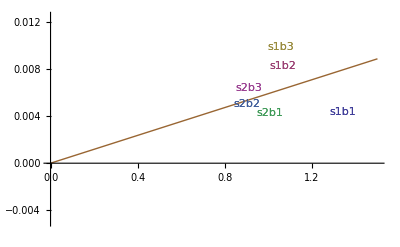

```mathematica
Show[smlPlot,pointsPlot]
```

## GMM Estimation

### The Code

### Mathematica Code

```mathematica
Dmat = ({{-1, -Total[rm]/n}, {-Total[rm]/n, -Total[rm^2]/n}});
x =Flatten[ ({{ConstantArray[1,n]}, {rm}}),1];
```

### GMM Results (Parameter Estimates and Standard Errors)

Note that in the below findings in each case newGamma_i stands for the (α_i, β_i) where 𝒾 is the portfolio. 
seAlpha_i stands for the standard error of the constant term and seBeta_i stands for the standard error of the data coefficient.

## Discussion

### 1.)

As was shown above, the parameter estimates were identical under OLS regression and GMM. This was the result we proved analytically and now have verified empirically. 

In many cases the standard errors are similar, but they are never actually exactly the same. This could be beecause there might be some autocorrelation in the data, because each portofolio has time series data for it. The good thing is that when the differ, usually the GMM estimators have the smaller standard error so that means that the parameter estimates are more efficient than those obtained through OLS.

### 2.)

It is interesting that for both of the stocks with low book to market ratios, the α term is negative.  A low B-M ratio is likely to mean that the underlying stocks are value stocks and on average they don’t outperform the market by a huge margin. 

Another interesting observation is that comparing the 3 B-M ratio stocks in the s1 group with their s2 counterpart, you see that β associated with the s1 stock is higher in each case. This could mean that smaller stocks are more sensitive to movements in the market. To further that line of thought, looking at the GMM standard errors accross the same group you see that the SE for each s1 stock is higher than that for the s2 group. That means that the s1 group of stocks is more volatile, providing further support for the hypothesis that the s1 stocks are more sensitive to movement in the market.

Another interesting thing to note is that regardless of size, as book to market ratio increases, the α of the portfolio increases. This means that the stocks for larger firms have higher average returns in a flat market. Saying the market is flat essentially negates the effect of the β coefficient in each case so the only thing driving returns is the intercept term α.